```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/FRENKEL_RESULTS/Tall/Frenkel_Tall"];
fileFFE={"e0.out.m","e0_FS.out.m","VFE.Fqh_FS.out.m","VFE.Fqh_Fel_FS.out.m","VFE.Fqh_Fel.out.m","VFE.Fqh.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number}],{i,1,4}];
```

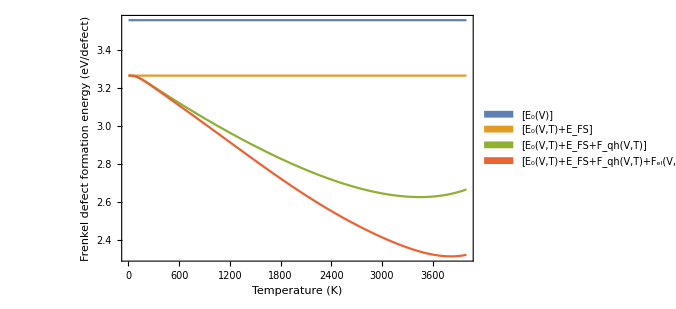

```mathematica
ListLinePlot[FFEdata,FrameLabel->{Style["Temperature (K)",12],Style["Frenkel defect formation energy (eV/defect)",12]},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"[E_0(V)]","[E_0(V,T)+_E_FS]","[E_0(V,T)+E_FS+F_qh(V,T)]","[E_0(V,T)+E_FS+F_qh(V,T)+F_el(V,T)]"}],{0.77,0.54}]]
```

```mathematica
(*Gibbs and temperature lists*)
gibbs=Transpose[FFEdata[[4]]][[2]];
ttemp=Transpose[FFEdata[[4]]][[1]];
(*Multiplicity*)
m1=24;m2=16;m3=4;
(*Trimer is lowest energy defect at 3.622, trimer is next 4.010 then 4.628 *)
deltaDimer=3.622-4.010
deltaTrimerUnbound=3.622-4.628
deltaDimerUnbound=3.622-4.688
```

```mathematica
(*Trimer concentration*)
tgibbsTrimer=Transpose@{ttemp,100*m1^0.5*Exp[-gibbs/(2*K2eV*ttemp)]};
(*Bound dimer*)
tgibbsDimer=Transpose@{ttemp,100*m1^0.5*Exp[-(gibbs-deltaDimer)/(2K2eV*ttemp)]};
(*Unbound trimer*)
tgibbsTrimerUnbound=Transpose@{ttemp,100*m2^0.5*Exp[-(gibbs-deltaTrimerUnbound)/(2K2eV*ttemp)]};
(*Unbound dimer*)
tgibbsDimerUnbound=Transpose@{ttemp,100*m3^0.5*Exp[-(gibbs-deltaDimerUnbound)/(2K2eV*ttemp)]};
(*Total*)
total=Transpose[{Transpose[tgibbsDimer][[1]],Transpose[tgibbsTrimer][[2]]+Transpose[tgibbsDimer][[2]]+Transpose[tgibbsTrimerUnbound][[2]]+Transpose[tgibbsDimerUnbound][[2]]}];
```

Power::infy: Infinite expression 1/0 encountered.

$Aborted

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0 encountered.

$Aborted

Power::infy: Infinite expression 1/0 encountered.

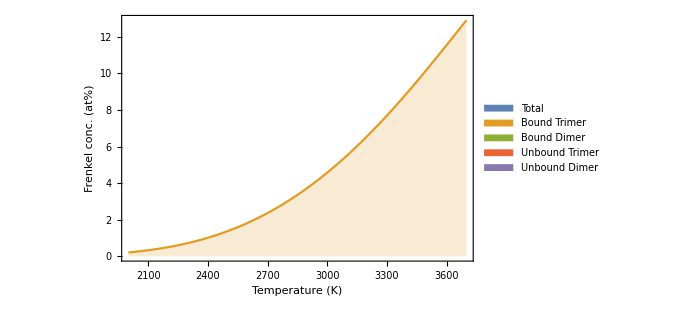

```mathematica
upper=3700;
lower=2000;
a=tgibbsTrimer[[lower;;upper]];
b=tgibbsDimer[[lower;;upper]];
c=tgibbsTrimerUnbound[[lower;;upper]];
d=tgibbsDimerUnbound[[lower;;upper]];
e=total[[lower;;upper]];

ListLinePlot[{e,a,b,c,d},Filling->Bottom,FrameLabel->{Style["Temperature (K)",12],Style["Frenkel conc. (at%)",12]},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"Total","Bound Trimer","Bound Dimer","Unbound Trimer","Unbound Dimer"}],{0.15,0.5}],PlotRange->All]
```